```mathematica
newAssoc[1102]
```

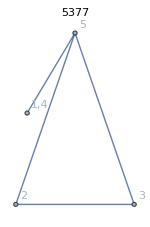
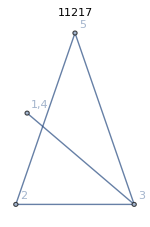
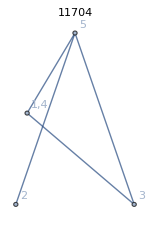
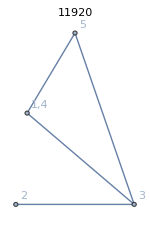
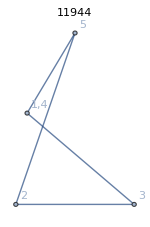
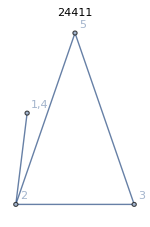
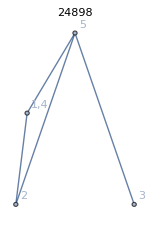
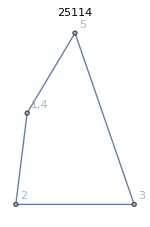

```mathematica
Table[Graph[newAssoc[key]["graph"],GraphLayout->"TutteEmbedding",VertexCoordinates->{},ImageSize->150,PlotLabel->key],{key,Select[Keys[newAssoc],With[{g=newAssoc[#]["graph"]},VertexCount[g]==4&&EdgeCount[g]==4]&&MemberQ[ newAssoc[#]["vertexsets"],{1,4}]&]}]
```

```mathematica
Table[Graph[newAssoc[key]["graph"],GraphLayout->"TutteEmbedding",VertexCoordinates->{},ImageSize->150,PlotLabel->key],{key,Select[Keys[newAssoc],With[{g=newAssoc[#]["graph"]},VertexCount[g]==4&&EdgeCount[g]==4]&&MemberQ[ newAssoc[#]["vertexsets"],{1,3}]&]}]
```

```mathematica
1,3->35977(α)
1,4->31681(β)
2,4->23041 (γ)
2,5-> 20803(δ)
3,5->27259 (ϵ)
```

```mathematica
CosyPrint2[23041]
```

-Graphics-   -Graphics-   x23041==x29602+x36166
x22312==x23041+x23770
x1171==x23041+x51472
x23041==x23044+x29608
x22789==x23041+x29857
x23013==x23041+x23072   (2 | 1 | 0 | 1 | 1
1 | 2 | 1 | 2 | 1
0 | 1 | 2 | 1 | 0
1 | 2 | 1 | 2 | 1
1 | 1 | 0 | 1 | 2){23041→b01/6+b04/6+b05/6-b07/6-b08/6-b10/6-b11/6-b14/6+b15/6-b16/6-b19/6-b20/3+b21/3+b24/3+b25/6-b26/6-b29/6-b30/6+b32/6+b33/6+b35/6+b36/12+b37/12+b38/12+b39/12-(5 b40)/12+b41/12+b42/12+b43/12+b44/12+b45/12+b46/12-b47/12-b48/12+b49/12-b50/4>0,}

```mathematica
TableForm[Table[key->(newAssoc[key]["colofour"]//CoeffVector//PerFive),{key,{35977,31681,23041,20803,27259}}]]
```

35977→{1/10,-1/10,-1/30,-2/15,1/6,-1/10,1/10,-1/60,1/12,-1/20}
31681→{1/10,-1/10,-1/30,-2/15,1/6,-1/10,1/10,-1/60,1/12,-1/20}
23041→{1/10,-1/10,-1/30,-2/15,1/6,-1/10,1/10,-1/60,1/12,-1/20}
20803→{1/10,-1/10,-1/30,-2/15,1/6,-1/10,1/10,-1/60,1/12,-1/20}
27259→{1/10,-1/10,-1/30,-2/15,1/6,-1/10,1/10,-1/60,1/12,-1/20}

```mathematica
TableForm[Table[key->(newAssoc[key]["colofour"]//CoeffVector),{key,{35977,31681,23041,20803,27259}}]]
```

35977→{1/6,1/6,0,0,1/6,-1/6,0,-1/6,-1/6,0,1/6,-1/6,0,0,-1/6,-1/3,-1/6,0,0,-1/6,1/6,1/3,0,0,1/3,-1/6,-1/6,0,0,-1/6,1/6,0,1/6,1/6,0,-5/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,-1/4,1/12,-1/12,-1/12,1/12,0}
31681→{0,1/6,1/6,1/6,0,-1/6,0,-1/6,0,-1/6,0,-1/6,1/6,-1/6,0,0,-1/6,-1/3,-1/6,0,0,1/3,1/6,1/3,0,0,-1/6,-1/6,-1/6,0,1/6,0,1/6,0,1/6,1/12,1/12,-5/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,-1/12,1/12,-1/4,1/12,-1/12,0}
23041→{1/6,0,0,1/6,1/6,0,-1/6,-1/6,0,-1/6,-1/6,0,0,-1/6,1/6,-1/6,0,0,-1/6,-1/3,1/3,0,0,1/3,1/6,-1/6,0,0,-1/6,-1/6,0,1/6,1/6,0,1/6,1/12,1/12,1/12,1/12,-5/12,1/12,1/12,1/12,1/12,1/12,1/12,-1/12,-1/12,1/12,-1/4,0}
20803→{1/6,1/6,1/6,0,0,0,-1/6,0,-1/6,-1/6,-1/6,1/6,-1/6,0,0,-1/6,-1/3,-1/6,0,0,1/3,1/6,1/3,0,0,-1/6,-1/6,-1/6,0,0,0,1/6,0,1/6,1/6,1/12,-5/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,1/12,-1/4,1/12,-1/12,-1/12,0}
27259→{0,0,1/6,1/6,1/6,-1/6,-1/6,0,-1/6,0,0,0,-1/6,1/6,-1/6,0,0,-1/6,-1/3,-1/6,0,0,1/3,1/6,1/3,0,0,-1/6,-1/6,-1/6,1/6,1/6,0,1/6,0,1/12,1/12,1/12,-5/12,1/12,1/12,1/12,1/12,1/12,1/12,-1/12,-1/12,1/12,-1/4,1/12,0}

```mathematica
Total[Table[newAssoc[key]["colofour"],{key,{35977,27259}}]]
```

b01/6+b02/6+b03/6+b04/6+b05/3-b06/3-b07/6-b08/6-b09/3+b11/6-b12/6-b13/6+b14/6-b15/3-b16/3-b17/6-b18/6-b19/3-b20/3+b21/6+b22/3+b23/3+b24/6+(2 b25)/3-b26/6-b27/6-b28/6-b29/6-b30/3+b31/3+b32/6+b33/6+b34/3-b36/3+b37/6+b38/6-b39/3+b40/6+b41/6+b42/6+b43/6+b44/6+b45/6-b46/3-b49/3+b50/6

```mathematica
Total[Table[newAssoc[key]["colofour"],{key,{35977,27259}}]]/.computedRep
```

289

```mathematica
Total[Table[newAssoc[key]["colofour"],{key,{27259,23041}}]]/.computedRep
```

188

```mathematica
Total[Table[newAssoc[key]["colofour"],{key,{23041,27259}}]]/.computedRep
```

188

```mathematica
x36166(α1)
x31738 (β1)
x29608 (γ1)
x36112(δ1),
x31714 (ϵ1)
```

```mathematica
Total[Table[newAssoc[key]["colofour"],{key,{36166,31738,29608,36112,31714}}]]
```

b01/2+b02/2+b03/2+b04/2+b05/2-b06/2-b07/2-b08/2-b09/2-b10/2-b11/3-b12/3-b13/3-b14/3-b15/3-b16/3-b17/3-b18/3-b19/3-b20/3+(2 b21)/3+(2 b22)/3+(2 b23)/3+(2 b24)/3+(2 b25)/3-b26/2-b27/2-b28/2-b29/2-b30/2+b31/2+b32/2+b33/2+b34/2+b35/2-(5 b36)/12-(5 b37)/12-(5 b38)/12-(5 b39)/12-(5 b40)/12+(7 b41)/12+(7 b42)/12+(7 b43)/12+(7 b44)/12+(7 b45)/12-b46/4-b47/4-b48/4-b49/4-b50/4

```mathematica
Total[Table[newAssoc[key]["colofour"],{key,{36166,31738,29608,36112,31714}}]]/.computedRep
```

239

```mathematica
CoeffVector[exp_]:=Table[Coefficient[ exp,v,1],{v,Sort[myVars]}]
```

```mathematica
Total[Table[newAssoc[key]["colofour"],{key,{36166,31738,29608,36112,31714}}]]-Total[Table[newAssoc[key]["colofour"],{key,{23041,27259}}]]//CoeffVector
```

{1/3,1/2,1/3,1/6,1/6,-1/3,-1/6,-1/3,-1/3,-1/3,-1/6,-1/3,-1/6,-1/3,-1/3,-1/6,-1/3,-1/6,1/6,1/6,1/3,2/3,1/3,1/6,1/6,-1/3,-1/2,-1/3,-1/6,-1/6,1/3,1/6,1/3,1/3,1/3,-7/12,-7/12,-7/12,-1/12,-1/12,5/12,5/12,5/12,5/12,5/12,-1/4,-1/12,-1/4,-1/12,-1/12,0}

```mathematica
PerFive[vect_]:=Table[Mean[Table[vect[[i+j]],{j,0,4}]],{i,1,Length[vect]-1,5}]
```

```mathematica
Total[Table[newAssoc[key]["colofour"],{key,{36166,31738,29608,36112,31714}}]]//CoeffVector//PerFive
```

{1/2,-1/2,-1/3,-1/3,2/3,-1/2,1/2,-5/12,7/12,-1/4}

```mathematica
Total[Table[newAssoc[key]["colofour"],{key,{36166,31738,29608,36112,31714}}]]//CoeffVector//PerFive//Sign
```

{1,-1,-1,-1,1,-1,1,-1,1,-1}

```mathematica
Total[Table[newAssoc[key]["colofour"],{key,{35977,27259}}]]//CoeffVector//PerFive
```

{1/5,-1/5,-1/15,-4/15,1/3,-1/5,1/5,-1/30,1/6,-1/10}

```mathematica
Total[Table[newAssoc[key]["colofour"],{key,{35977,27259}}]]//CoeffVector//PerFive//Sign
```

{1,-1,-1,-1,1,-1,1,-1,1,-1}

```mathematica
Total[Table[newAssoc[key]["colofour"],{key,{27259}}]]//CoeffVector//PerFive//Sign
```

{1,-1,-1,-1,1,-1,1,-1,1,-1}

```mathematica
kkk=1
```

```mathematica
Monitor[kkk=1;Table[computed[newAssoc[key]["colofour"]]={3728,2520,3000,2488,1280,2852,1940,2852,2324,1292,2348,1590,1268,1108,264,2384,1596,1848,1500,712,2616,2120,1996,1682,894,1112,702,2640,1772,2038,2050,912,1112,870,976,746,224,2360,1558,1924,1598,796,980,672,1060,870,230,980,628,186,182}[[kkk]];kkk+=1,{key,Select[Keys[newAssoc],MemberQ[myVars,newAssoc[#]["colofour"]]&]}],key]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52}

```mathematica
computed=Association[]
```

<||>

```mathematica
computed
```

<||>

```mathematica
computedRep = Table[key->computed[key],{key,Keys[computed]}]//Sort
```

{b01→2640,b02→2852,b03→2616,b04→3000,b05→2852,b06→2520,b07→2488,b08→2348,b09→2360,b10→2384,b11→2120,b12→2324,b13→2050,b14→2038,b15→1996,b16→1772,b17→1940,b18→1682,b19→1924,b20→1848,b21→1596,b22→1590,b23→1598,b24→1500,b25→1558,b26→1292,b27→976,b28→1268,b29→1060,b30→1112,b31→980,b32→980,b33→1112,b34→1280,b35→1108,b36→628,b37→672,b38→702,b39→796,b40→712,b41→912,b42→746,b43→894,b44→870,b45→870,b46→224,b47→264,b48→182,b49→186,b50→230,z→3728}

```mathematica
Select[Keys[newAssoc],newAssoc[#]["comp"]==Greater&]//Length
```

813

```mathematica
Select[Keys[newAssoc],newAssoc[#]["comp"]==GreaterEqual&]//Length
```

1082

```mathematica
Length[newAssoc]
```

1895

```mathematica
Table[newAssoc[key]["comp"],{key,Keys[newAssoc]}]
```

```mathematica
Select[Keys[newAssoc],newAssoc[#]["colofour"]==z&]
```

{0}

```mathematica
Plot3D[
With[
{c=-a/3,d=-a/3},
a(b01+b02+b03+b04+b05)+b(b06+b07+b08+b09+b10)+c(+b11+b12+b13+b14+b15)+d(b16+b17+b18+b19+b20)/.computedRep],
{a,0,1},{b,-1,0}, AxesLabel->{a,b}]
```

-Graphics3D-

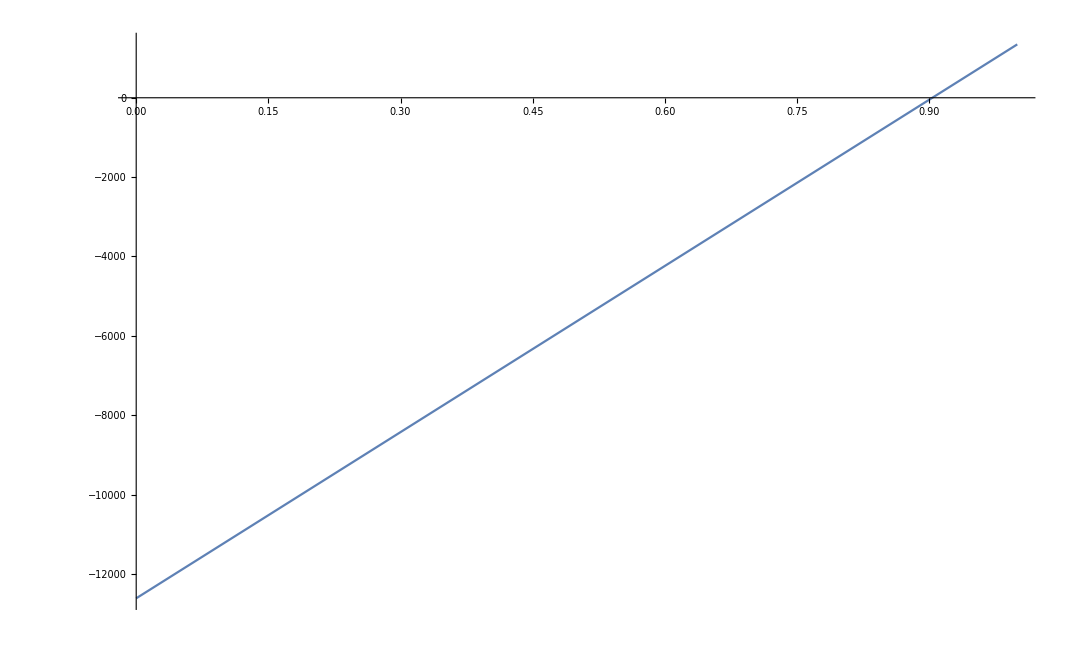

```mathematica
Plot[
With[
{b=-1/2,c=-1/3,d=-1/3},
a(b01+b02+b03+b04+b05)+b(b06+b07+b08+b09+b10)+c(+b11+b12+b13+b14+b15)+d(b16+b17+b18+b19+b20)/.computedRep]
,{a,0,1}]
```

```mathematica
With[
{a=1/5,b=-1/5,c=-1/15,d=-4/15},
a(b01+b02+b03+b04+b05)+b(b06+b07+b08+b09+b10)+c(+b11+b12+b13+b14+b15)+d(b16+b17+b18+b19+b20)/.computedRep]//N
```

-2774.13

```mathematica
With[
{a=1/2,b=-1/2,c=-1/3,d=-1/3},
a(b01+b02+b03+b04+b05)+b(b06+b07+b08+b09+b10)+c(+b11+b12+b13+b14+b15)+d(b16+b17+b18+b19+b20)/.computedRep]//N
```

-5634.67

```mathematica
With[
{a=2/3,b=-1/2},
a(b21+b22+b23+b24+b25)+b(b26+b27+b28+b29+b30)/.computedRep]//N
```

2374.

```mathematica
With[
{a=1/3,b=-1/5},
a(b21+b22+b23+b24+b25)+b(b26+b27+b28+b29+b30)/.computedRep]//N
```

1472.4